# Compiling Matmul to Blocks and Tiles, Version 2

## Technical Report, Preliminary Draft, GSI Technology

Brian Beckman
Technology Fellow
November, 2023

## Abstract

The layout problem answers “how to rearrange matrices to fit the APU?” Consider domain matrices, A[m,k] and B[k,n], of arbitrary but compatible dimensions, meaning that the column count, k, of A equals the row count, k, of B. Due to compatibility, the matrix product A.B is sensible. Now consider the Gemini-I APU, which has a main memory (MMB) of 24×VR bits, where a VR is 64 HBs and an HB (half-bank) is 2048×16 bits. The Gemini-I APU also has 53 VRs worth of space in L1 cache (parity off). The layout problem for matrix multiplication is finding an optimal procedure for dynamically loading to, multiplying in, and storing from chunks of A and B in the APU’s L1 cache and main memory. The solution to the layout problem includes finding optimal sizes of chunks and optimal sequences of operations for moving and multiplying data. Optimal means minimum running time. Compile time is not considered. Running time includes the time for I/O between L1 and main memory.

At first glance, the layout problem seems like a constrained combinatorial optimization problem, thus difficult to pose well and expensive to solve. This paper by Kuzma et al. presents an approach wherein the compiler breaks up input domain matrices into blocks and tiles. Blocks are optimized to fit L1, tiles are optimized to fit main memory, where multiplication occurs. We investigate and mechanize Kuzma’s algorithm in this paper, first by reproducing Kuzma’s original example, then by adapting that example to the APU.

## Accumulated Outer Product

First, we note that accumulated outer product is preferable to iterated inner product for all dimensions >1. This fact justifies the inner-most routine shown below, tileMul.

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
```

### Large Matrices

```mathematica
On[Assert];
```

```mathematica
ClearAll[timings];
(timings=With[{precision=1.*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,200,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 5.×10^-6 s | 0.000017 s | 0.000012 s
26 | 0.000018 s | 0.001684 s | 0.000081 s
51 | 0.000013 s | 0.007965 s | 0.000225 s
76 | 0.000241 s | 0.026589 s | 0.000637 s
101 | 0.00006 s | 0.063752 s | 0.001698 s
126 | 0.000071 s | 0.113922 s | 0.003041 s
151 | 0.000087 s | 0.173122 s | 0.003815 s
176 | 0.000348 s | 0.305297 s | 0.004737 s)

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

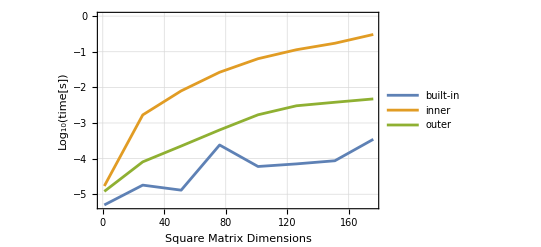

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```

## Table 1 — VSR and ACC

Kuzma presents a worked-out example for his IBM POWER10 MMA chip, which has VSRs of 128 bits and ACCs of 512 bits. The bits in these registers can handle seven different types of elements.

```mathematica
ClearAll[mmaI,mmaI4,mmaI8,mmaI16,mmaBf16,mmaF16,mmaF32,mmaF64];
```

The integer MMA instructions for the POWER10 consume four 128-bit VSRs — an ACC, for a total of 512 bits. Up to 32 VSRs can be used, 4 at a time, in this way.

```mathematica
mmaI[bitCount_?(MemberQ[{4,8,16},#]&)]:=
With[{m=4,k=32/bitCount,n=4},
With[{A=RandomInteger[{0,2^bitCount-1},{m,k}],
B=RandomInteger[{0,2^bitCount-1},{k,n}]},
accumulatedOuterProduct[m,k,n,A,B]]]
```

```mathematica
mmaI[8]
```

<|m→4,k→4,n→4,result→{{66708,81090,53226,66894},{93391,87949,77167,66791},{58967,73132,52862,59159},{77830,82236,51364,60610}},time→0.000022 s|>

accumulatedOuterProduct also works as a rank-1 outer product.

```mathematica
accumulatedOuterProduct[5,1,4,({{1}, {2}, {3}, {4}, {5}}),({{7, 11, 13, 19}})]["result"]//MatrixForm
```

(7 | 11 | 13 | 19
14 | 22 | 26 | 38
21 | 33 | 39 | 57
28 | 44 | 52 | 76
35 | 55 | 65 | 95)

## Codegen for GEMM

GEMM is a standard operation in LAPACK.

### Algorithm 1

A, B, APack, BPack, AccTile, ATile, BTile, ABTile, CTile, and CNewTile are free-variable pointers to memory. nr , kr, mr are free packing parameters. In my opinion, they would be better called tiling parameters because they’re tuned to the intrinsic LLVM on line 12, but I’ll follow the paper’s nomenclature for now. nc, kc, mc are free blocking parameters that divide matrices into blocks appropriately sized and ordered (row-major versus column-order) for cache. lda, ldb, ldc are free leading dimensions, thus strides, and pertain to either row-major or column-major storage conventions. The pack function reorders blocks into row-major or column-major order as needed for optimal tile-multiplication speed. α and β are free scalar parameters required by GEMM.

```mathematica
ClearAll[packingParameters,mr,kr,nr,blockingParameters,mc,kc,nc,A,APack,B,BPack,leadingDimensions,lda,ldb,ldc,ATile,BTile,AccTile,ABTile,CTile,CNewTile,β,α];
packingParameters={mr,kr,nr};
blockingParameters={mc,kc,nc};
leadingDimensions={lda,ldb,ldc};
```

M, K, N are original dimensions: M×K for AOriginal, K×N for BOriginal. kc (block size) must divide K; mc (block size) must divide M, nc (block size) must divide N. If not, the original matrices, AOriginal and BOriginal, must be padded out with zeros to integer multiples of mc, kc, nc. Such is preprocessing, not described here.

In the following illustration, AOriginal and BOriginal are stored in column-major order.

Let us mechanize a concrete version of this illustration by ignoring most ellipses (triple dots). An exception is the picture of B, for which we increase kc from 2kr to 3kr for consistency with the picture of A. The two pictures for A and for B represent the (4,2) and (2,2) 1-indexed blocks, respectively, of the original matrices, AOriginal and BOriginal.

## Compiling MatMul to Blocks and Tiles

### tileMul

Everything gets compiled to calls of tileMul.

tileMul multiplies blocks that contain small tiles, multiplying each tile at maximum speed in the machine. A tile is a sub-matrix that snugly fits in the particular machine registers that are necessary for multiplication. tileMul is here parameterized to the dimensions of blocks and tiles so that we can compile to various devices, such as the Gemini-I APU and the Gemini-II APU, which differ in dimensions.

tileMul takes a pair of blocks with tiles inside, then triples of integers for inner and outer dimensions. The three outer dimensions, mc, kc, and nc, correspond to the dimensions of block multiplicands, mc×kc and kc×nc. The three inner dimensions, mr, kr, and nr, correspond to dimensions of tile multiplicands, namely mr×kr and kr×nr. Each outer dimension must be evenly divisible by the corresponding inner dimension, meaning that tiles must fit blocks with no gaps or overlaps. The number of block rows must be an integer multiple of the number of tile rows, and likewise for columns. Each of mc/mr, kc/kr, and nc/nr must be integers.

As an illustration, consider the following two tiled blocks.

```mathematica
aBlockTiled$=({{({{15, 14, 10, 15}, {3, 9, 8, 5}}), ({{6, 0, 3, 8}, {5, 10, 9, 6}}), ({{3, 14, 1, 1}, {6, 1, 14, 4}})}, {({{11, 14, 9, 10}, {11, 13, 3, 3}}), ({{12, 2, 0, 15}, {5, 3, 15, 13}}), ({{5, 4, 14, 1}, {13, 4, 7, 3}})}, {({{12, 7, 14, 14}, {15, 6, 14, 13}}), ({{2, 7, 15, 15}, {1, 13, 0, 8}}), ({{5, 0, 9, 1}, {14, 5, 2, 10}})}});
bBlockTiled$=({{({{9, 4}, {4, 1}, {11, 9}, {15, 3}}), ({{9, 13}, {14, 12}, {9, 13}, {12, 13}}), ({{6, 7}, {7, 11}, {10, 3}, {7, 15}}), ({{12, 3}, {8, 4}, {0, 13}, {3, 12}}), ({{4, 11}, {8, 11}, {5, 4}, {5, 5}})}, {({{13, 15}, {14, 2}, {0, 13}, {10, 0}}), ({{7, 0}, {10, 15}, {3, 15}, {8, 7}}), ({{1, 4}, {6, 6}, {15, 6}, {11, 7}}), ({{15, 5}, {11, 6}, {15, 6}, {11, 11}}), ({{5, 8}, {14, 10}, {8, 15}, {5, 15}})}, {({{3, 14}, {10, 10}, {7, 5}, {10, 8}}), ({{0, 3}, {14, 5}, {6, 1}, {0, 3}}), ({{5, 3}, {9, 7}, {13, 2}, {14, 12}}), ({{5, 2}, {11, 15}, {1, 10}, {7, 5}}), ({{9, 12}, {11, 0}, {2, 7}, {8, 6}})}});
```

The outer dimensions of the pair (aBlockTiled$, bBlockTiled$) are mc=(3×(mr=2))=6 (three rows of 2-row tiles in aBlockTiled$), kc=(3×(kr=4))=12 (three columns of 4-column tiles in aBlockTiled$, and three rows of 4-row tiles in bBlockTiled$), and nc=(5×(nr=2))=10 (five columns of 2-column tiles in bBlockTiled$). The inner dimensions are mr=2, kr=4, nr=2, corresponding respectively to the row dimension, mr, of a left-multiplicand tile; to the column dimension, kr, of a left-multiplicand tile, equal to the row dimension of a right-multiplicand tile; and to the column dimension, nr, of a right-multiplicand tile.

Notice that nr must equal mr because tiles are of transposed shapes on the left and the right of a tile product. The API has separate parameters for them for the sake of symmetry in the API, making it easier to remember.

Let’s define tileMul as an iterated inner product of tiles and accumulated outer product within the tiles, then apply it to these examples:

```mathematica
ClearAll[tileMul];
tileMul[ATiles_,BTiles_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{tm,tk,tn,CTile,McByMr=mc/mr,KcByKr=kc/kr,NcByNr=nc/nr},
CTile=ConstantArray[ConstantArray[0,{mr,nr}],{McByMr,NcByNr}];
For[tm=1,tm<=McByMr,tm++,(* for each row of A's tiles *)
For[tn=1,tn<=NcByNr,tn++,(* for each column in B's tiles *)
For[tk=1,tk<=KcByKr,tk++,(* iterated inner products of tiles *)
(* ATiles⟦tm,tk⟧.BTiles⟦tk,tn⟧ implicitly by accumulated outer product *)
CTile[[tm,tn]]+=ATiles[[tm,tk]].BTiles[[tk,tn]]]]];
CTile];
```

```mathematica
tileMul[aBlockTiled$,bBlockTiled$,6,12,10,2,4,2]//MatrixForm
```

((850 | 533
657 | 516) | (918 | 872
593 | 692) | (700 | 733
739 | 496) | (737 | 778
592 | 601) | (582 | 696
541 | 748)
(901 | 541
624 | 650) | (860 | 745
656 | 813) | (770 | 656
833 | 610) | (731 | 778
858 | 607) | (539 | 866
629 | 1004)
(862 | 585
989 | 608) | (803 | 1066
784 | 968) | (949 | 703
811 | 747) | (780 | 826
710 | 751) | (618 | 1000
735 | 852))

To check this result against a straightforward matrix product, we must flatten the tile level.

### untileBlock

Is the result above equivalent to the matrix product aBlockTiled$.bBlockTiled$? First define untileBlock, which does exactly what its name says.

```mathematica
ClearAll[untileBlock];
untileBlock[ATiledBlock_,mr_,mc_,kr_,kc_]:=
(* Produce 1 mc×kc block from its tiles, each mr×kr. *)
Module[{ABlock=ConstantArray[0,{mc,kc}],tileI,tileJ,inI,inJ,bm,bk},
For[bm=1,bm<=mc,bm++,
For[bk=1,bk<=kc,bk++,
tileI=1+Quotient[(bm-1),mr];
tileJ=1+Quotient[(bk-1),kr];
inI=1+Mod[(bm-1),mr];
inJ=1+Mod[(bk-1),kr];
ABlock[[bm,bk]]=ATiledBlock[[tileI,tileJ,inI,inJ]]]];
ABlock];
```

Apply untileBlock to aBlockTiled$ and to bBlockTiled$., compute the matrix product via Wolfram’s built-in, then visually check that the untiled matrices match their tiled brethren above.

```mathematica
(aBlock$=untileBlock[aBlockTiled$,2,6,4,12])//MatrixForm
(bBlock$=untileBlock[bBlockTiled$,4,12,2,10])//MatrixForm
(cBlock$=aBlock$.bBlock$)//MatrixForm
```

(15 | 14 | 10 | 15 | 6 | 0 | 3 | 8 | 3 | 14 | 1 | 1
3 | 9 | 8 | 5 | 5 | 10 | 9 | 6 | 6 | 1 | 14 | 4
11 | 14 | 9 | 10 | 12 | 2 | 0 | 15 | 5 | 4 | 14 | 1
11 | 13 | 3 | 3 | 5 | 3 | 15 | 13 | 13 | 4 | 7 | 3
12 | 7 | 14 | 14 | 2 | 7 | 15 | 15 | 5 | 0 | 9 | 1
15 | 6 | 14 | 13 | 1 | 13 | 0 | 8 | 14 | 5 | 2 | 10)

(9 | 4 | 9 | 13 | 6 | 7 | 12 | 3 | 4 | 11
4 | 1 | 14 | 12 | 7 | 11 | 8 | 4 | 8 | 11
11 | 9 | 9 | 13 | 10 | 3 | 0 | 13 | 5 | 4
15 | 3 | 12 | 13 | 7 | 15 | 3 | 12 | 5 | 5
13 | 15 | 7 | 0 | 1 | 4 | 15 | 5 | 5 | 8
14 | 2 | 10 | 15 | 6 | 6 | 11 | 6 | 14 | 10
0 | 13 | 3 | 15 | 15 | 6 | 15 | 6 | 8 | 15
10 | 0 | 8 | 7 | 11 | 7 | 11 | 11 | 5 | 15
3 | 14 | 0 | 3 | 5 | 3 | 5 | 2 | 9 | 12
10 | 10 | 14 | 5 | 9 | 7 | 11 | 15 | 11 | 0
7 | 5 | 6 | 1 | 13 | 2 | 1 | 10 | 2 | 7
10 | 8 | 0 | 3 | 14 | 12 | 7 | 5 | 8 | 6)

(850 | 533 | 918 | 872 | 700 | 733 | 737 | 778 | 582 | 696
657 | 516 | 593 | 692 | 739 | 496 | 592 | 601 | 541 | 748
901 | 541 | 860 | 745 | 770 | 656 | 731 | 778 | 539 | 866
624 | 650 | 656 | 813 | 833 | 610 | 858 | 607 | 629 | 1004
862 | 585 | 803 | 1066 | 949 | 703 | 780 | 826 | 618 | 1000
989 | 608 | 784 | 968 | 811 | 747 | 710 | 751 | 735 | 852)

### blockIt, tileIt

We now know how to multiply blocks full of snug tiles. We need, from general matrices, to produce matrices full of snug blocks, in-turn full of snug tiles. The dimensions of the snug blocks must divide the dimensions of the matrices, but that is the only restriction. If the matrices don’t snugly contain blocks, pad out the matrices in a pre-processing step. We do not consider that padding step in this paper.

Define a pair of functions, blockIt and tileIt, that, respectively, produce a blocked matrix and a tiled block.

```mathematica
ClearAll[blockIt,tileIt];

blockIt[A_,mc_,M_,kc_,K_]:=Table[
A[[m;;m+mc-1,k;;k+kc-1]],{m,1,M,mc},{k,1,K,kc}];

tileIt[ABlock_,mr_,mc_,kr_,kc_]:=Table[
ABlock[[m;;m+mr-1,k;;k+kr-1]],{m,1,mc,mr},{k,1,kc,kr}];
```

Iterate tileIt over the result of blockIt on a matrix to get a fully blocked and tiled matrix. Below is an example. Notice we build the dimensions bottom-up to ensure integer divisibility and avoid padding. The regular structure in the displays is evident and instructive. Strive to see how 2D iterations of tileMul produces desired results.

```mathematica
With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=2mr,kc=2kr,nc=2nr},(* mc=4, kc=8, nc=4 -- blocks *)
With[{M=2mc,K=2kc,N=2nc},(* M=8, K=16, N=8, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocked=blockIt[A,mc,M,kc,K],
BBlocked=blockIt[B,kc,K,nc,N],
ATiled,BTiled},
ATiled=Table[tileIt[ABlocked[[bm,bk]],mr,mc,kr,kc],{bm,1,M/mc},{bk,1,K/kc}];
BTiled=Table[tileIt[BBlocked[[bk,bn]],kr,kc,nr,nc],{bk,1,K/kc},{bn,1,N/nc}];
Column[{(* displays *)
ATiled//MatrixForm,
BTiled//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[A_blocked]"->Dimensions[ABlocked],
"dim[B_blocked]"->Dimensions[BBlocked],
"A_tiled"->Dimensions[ATiled],
"B_tiled"->Dimensions[BTiled],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{8,16},dim[B]→{16,8},dim[A_blocked]→{2,2,4,8},dim[B_blocked]→{2,2,8,4},A_tiled→{2,2,2,2,2,4},B_tiled→{2,2,2,2,4,2},bits→4,mr→2,kr→4,nr→2,mc→4,kc→8,nc→4,M→8,K→16,N→8|>

(((3 | 2 | 2 | 0
6 | 0 | 14 | 0) | (9 | 4 | 11 | 15
4 | 9 | 7 | 15)
(2 | 12 | 8 | 3
6 | 10 | 5 | 12) | (14 | 9 | 1 | 6
6 | 2 | 13 | 2)) | ((3 | 12 | 13 | 6
2 | 9 | 6 | 10) | (3 | 3 | 6 | 10
13 | 14 | 13 | 9)
(14 | 10 | 0 | 4
9 | 10 | 15 | 14) | (14 | 1 | 5 | 1
15 | 2 | 1 | 9))
((3 | 2 | 15 | 15
5 | 7 | 13 | 4) | (15 | 14 | 3 | 6
15 | 5 | 6 | 14)
(0 | 7 | 11 | 11
2 | 9 | 11 | 13) | (7 | 14 | 12 | 12
15 | 3 | 5 | 10)) | ((7 | 14 | 2 | 3
14 | 1 | 5 | 1) | (14 | 5 | 5 | 4
3 | 13 | 13 | 5)
(13 | 10 | 2 | 6
14 | 3 | 0 | 4) | (3 | 4 | 9 | 15
13 | 8 | 15 | 11)))
(((7 | 11
15 | 2
4 | 10
14 | 12) | (10 | 5
12 | 4
12 | 0
1 | 8)
(1 | 9
7 | 10
10 | 2
13 | 4) | (15 | 0
11 | 15
8 | 4
13 | 12)) | ((5 | 10
0 | 12
2 | 3
15 | 6) | (15 | 11
9 | 1
15 | 7
10 | 2)
(15 | 4
15 | 10
13 | 13
9 | 9) | (4 | 12
0 | 3
13 | 5
10 | 2))
((15 | 13
5 | 8
5 | 12
4 | 8) | (0 | 0
11 | 2
7 | 3
5 | 11)
(15 | 13
0 | 5
15 | 14
7 | 6) | (14 | 2
3 | 1
13 | 11
14 | 7)) | ((6 | 3
7 | 11
2 | 9
10 | 0) | (9 | 13
2 | 14
4 | 2
0 | 15)
(0 | 9
10 | 2
11 | 11
1 | 10) | (8 | 5
3 | 1
2 | 11
2 | 11)))

### unBlock

unBlock is exactly parallel to untileBlock. It does not need a unit test or an illustrative example.

```mathematica
ClearAll[unblock];

unblock[ABlocked_,mc_,M_,kc_,K_]:=
Module[{A=ConstantArray[0,{M,K}],blockI,blockJ,inI,inJ,m,k},
For[m=1,m<=M,m++,
For[k=1,k<=K,k++,
blockI=1+Quotient[(m-1),mc];
blockJ=1+Quotient[(k-1),kc];
inI=1+Mod[(m-1),mc];
inJ=1+Mod[(k-1),kc];
A[[m,k]]=ABlocked[[blockI,blockJ,inI,inJ]]]];
A];
```

### blockTileMul, blockMul

blockTileMul is the intermediate target of compilation, after matrices have been blocked and tiled as described above. blockTileMul calls tileMul at bottom.

For testing, we include a blockMul routine for blocked-but-not-tiled matrices: the untiled results of blockTileMul must match the results of blockMul, and the unblocked results must match the results of Mathematica’s built-in matrix multiplication. The following defines blockTileMul and blockMul, then Asserts the requirements on an example.

```mathematica
On[Assert];
ClearAll[blockMul,blockTileMul];

blockTileMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
(* ABlocks is an array of mc×kc blocks, BBlock of kc×nc blocks. *)
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CTiled,ATiles,BTiles},
CTiled=ConstantArray[ConstantArray[ConstantArray[0,{mr,nr}],
{McByMr,NcByNr}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* iterated inner product *)
For[bk=1,bk<=KByKc,bk++,
ATiles=tileIt[ABlocks[[bm,bk]],mr,mc,kr,kc];
BTiles=tileIt[BBlocks[[bk,bn]],kr,kc,nr,nc];
CTiled[[bm,bn]]+=tileMul[ATiles,BTiles,mc,kc,nc,mr,kr,nr]]]];
CTiled];

blockMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CBlocked},
CBlocked=ConstantArray[ConstantArray[0,{mc,nc}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* iterated inner product *)
For[bk=1,bk<=KByKc,bk++,
CBlocked[[bm,bn]]+=ABlocks[[bm,bk]].BBlocks[[bk,bn]]]]];
CBlocked];

With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=6, kc=12, nc=10 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=30, K=36, N=30, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
A//MatrixForm;
ABlocks//MatrixForm;
BBlocks//MatrixForm;
CTiled//MatrixForm,
CBlockedCheck//MatrixForm;
CBlocked//MatrixForm;
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;
(*griddit[A,mc,M,kc,K],*)
(*griddit[B,kc,K,nc,N]*)}]]]]]]]
```

<|dim[A]→{30,36},dim[B]→{36,30},dim[C_tiled]→{5,3,3,5,2,2},dim[A_blocks]→{5,3,6,12},dim[B_blocks]→{3,3,12,10},dim[C]→{30,30},bits→4,mr→2,kr→4,nr→2,mc→6,kc→12,nc→10,M→30,K→36,N→30|>

(((1867 | 1960
1660 | 1517) | (2027 | 2007
2015 | 1777) | (2386 | 1714
2269 | 1659) | (1480 | 2287
1402 | 2207) | (2018 | 2486
2215 | 2249)
(1860 | 1801
1970 | 1706) | (2081 | 2092
1898 | 1948) | (2362 | 1846
2315 | 1687) | (1581 | 2523
1737 | 2255) | (1911 | 2645
2163 | 2665)
(1806 | 1861
1780 | 1674) | (2127 | 2208
2003 | 1969) | (2577 | 1866
1753 | 1618) | (1837 | 2403
1520 | 1986) | (2453 | 2629
1948 | 2201)) | ((1815 | 1522
1733 | 1316) | (1974 | 1828
2028 | 1994) | (2027 | 2276
1865 | 2137) | (1869 | 1608
1720 | 1626) | (1916 | 1785
1682 | 1911)
(1955 | 1799
1820 | 1648) | (2116 | 2002
1972 | 1983) | (2190 | 2551
2111 | 2300) | (1641 | 1673
1887 | 2070) | (1664 | 1882
1727 | 2152)
(2031 | 2065
1433 | 1555) | (2080 | 2087
1555 | 1592) | (2355 | 2601
1766 | 2158) | (1958 | 1928
1564 | 1641) | (1791 | 2065
1515 | 1574)) | ((1873 | 1923
1943 | 1986) | (2304 | 1930
2597 | 2121) | (1663 | 2021
1567 | 2195) | (2120 | 1756
1971 | 1886) | (1602 | 2009
1599 | 2079)
(1931 | 1860
1812 | 1989) | (2635 | 2036
2637 | 2296) | (1735 | 2454
1781 | 2280) | (2030 | 1905
2221 | 2009) | (1839 | 2051
1947 | 2123)
(2130 | 2096
1928 | 1676) | (2804 | 2293
2080 | 1924) | (1875 | 2542
1634 | 2102) | (2115 | 2166
2012 | 1603) | (1966 | 2534
1328 | 1962))
((2156 | 1907
1815 | 1656) | (1782 | 1760
1922 | 1744) | (2362 | 1784
2020 | 1712) | (1690 | 2129
1554 | 1904) | (2313 | 2385
2096 | 1936)
(2413 | 2230
1924 | 1733) | (2249 | 2564
1901 | 1968) | (2688 | 2289
2119 | 1785) | (2120 | 2880
1507 | 2288) | (2643 | 2895
1981 | 2481)
(2460 | 2041
1729 | 1756) | (2227 | 2278
1666 | 1734) | (2797 | 2237
1851 | 1612) | (2016 | 2608
1593 | 2055) | (2728 | 2878
1764 | 2153)) | ((1775 | 1698
1716 | 1457) | (2087 | 1790
1824 | 1816) | (2257 | 2297
1966 | 1892) | (2074 | 2013
1694 | 1477) | (1969 | 1850
1453 | 1653)
(2187 | 2042
1795 | 1519) | (2558 | 2246
2142 | 1984) | (2472 | 3064
2032 | 2338) | (2311 | 2242
1911 | 1721) | (2130 | 2059
1742 | 1906)
(2109 | 1955
1715 | 1470) | (2407 | 2129
1845 | 1521) | (2516 | 2899
1873 | 1718) | (2240 | 2352
1662 | 1427) | (2253 | 2266
1535 | 1669)) | ((1924 | 1808
1845 | 1864) | (2654 | 2071
2356 | 1866) | (1952 | 2187
1475 | 1988) | (1969 | 1927
1878 | 1873) | (1834 | 2068
1657 | 1822)
(2353 | 2275
1963 | 1741) | (3257 | 2675
2368 | 2067) | (2172 | 2711
1734 | 2277) | (2313 | 2184
1921 | 1801) | (2015 | 2459
1558 | 2091)
(2395 | 2245
1700 | 1552) | (3174 | 2733
2468 | 1674) | (2116 | 2663
1474 | 2112) | (2270 | 2245
1821 | 1933) | (2198 | 2529
1511 | 1961))
((1875 | 1816
1953 | 1897) | (2070 | 1911
2207 | 2330) | (2037 | 1812
2228 | 1821) | (1619 | 2469
1718 | 2536) | (2344 | 2174
2485 | 2668)
(1772 | 1679
1755 | 1706) | (1942 | 1730
1997 | 2085) | (2156 | 1709
2219 | 1833) | (1491 | 2160
1834 | 2175) | (2038 | 2038
2178 | 2664)
(2107 | 1931
1826 | 1698) | (2138 | 2194
1905 | 1718) | (2470 | 1912
2055 | 1710) | (1712 | 2592
1681 | 2023) | (2289 | 2787
2104 | 1987)) | ((1747 | 1866
2026 | 1750) | (1993 | 2101
1925 | 2013) | (2236 | 2270
2435 | 2464) | (1989 | 1808
1993 | 1725) | (1695 | 1976
1819 | 1943)
(1529 | 1642
1723 | 1948) | (1807 | 1648
1897 | 2070) | (1993 | 2160
2152 | 2433) | (1614 | 1718
1749 | 2077) | (1410 | 1894
1741 | 2081)
(2017 | 1890
1557 | 1556) | (2214 | 1865
1799 | 1734) | (2302 | 2610
2170 | 1810) | (2021 | 1828
1703 | 1557) | (1889 | 1931
1360 | 1784)) | ((2180 | 2031
2196 | 2125) | (2791 | 2181
2940 | 2278) | (1732 | 2448
1814 | 2508) | (1851 | 1872
2255 | 2152) | (1602 | 2319
1810 | 2373)
(1721 | 1854
1859 | 1885) | (2382 | 1869
2512 | 2426) | (1694 | 2088
1853 | 2659) | (1976 | 1770
2087 | 1871) | (1750 | 1750
1794 | 2381)
(2234 | 2027
1842 | 1795) | (2954 | 2494
2415 | 1844) | (1914 | 2321
1370 | 2225) | (2327 | 2023
1880 | 2110) | (1686 | 2282
1519 | 2283))
((2090 | 2021
1817 | 1629) | (2299 | 2130
1925 | 1765) | (2526 | 2019
1889 | 1791) | (2027 | 2562
1605 | 2180) | (2569 | 2485
2161 | 2000)
(1885 | 1808
1877 | 2001) | (1719 | 1853
1811 | 1964) | (2098 | 1627
2537 | 1954) | (1370 | 1985
1834 | 2488) | (1936 | 2116
2177 | 2314)
(1660 | 1834
1547 | 1413) | (1767 | 2173
1621 | 1785) | (2098 | 1791
1649 | 1541) | (1781 | 2364
1448 | 1719) | (2212 | 2316
1940 | 2022)) | ((2102 | 1821
1506 | 1345) | (2209 | 2085
1798 | 1785) | (2449 | 2419
1972 | 2009) | (2153 | 1941
1569 | 1522) | (2100 | 2123
1708 | 1526)
(1792 | 1383
2078 | 1758) | (2009 | 1695
2311 | 1868) | (1772 | 1954
2082 | 2396) | (1880 | 1684
2036 | 1851) | (1690 | 1721
1902 | 1956)
(1982 | 1674
1436 | 1320) | (1961 | 1892
1640 | 1594) | (2022 | 2299
1840 | 1743) | (1911 | 1756
1576 | 1472) | (1894 | 1595
1300 | 1538)) | ((2361 | 2270
2021 | 2009) | (3051 | 2424
2330 | 1968) | (1925 | 2365
1594 | 2006) | (2300 | 2385
1773 | 1782) | (2135 | 2521
1599 | 2064)
(1699 | 1610
2045 | 1957) | (2420 | 1899
2937 | 2280) | (1632 | 2006
1808 | 2173) | (1853 | 1623
2083 | 2175) | (1409 | 1770
1882 | 2053)
(2127 | 1712
1689 | 1649) | (2763 | 2163
2274 | 1926) | (1804 | 2216
1312 | 1818) | (1933 | 2105
1584 | 1671) | (1759 | 2110
1373 | 1905))
((2207 | 2201
1928 | 1798) | (2119 | 1987
1905 | 1900) | (2448 | 1919
2116 | 1510) | (1987 | 2423
1366 | 1828) | (2515 | 2431
2269 | 2534)
(2031 | 1689
1827 | 1511) | (2044 | 1926
1890 | 1774) | (2435 | 1730
2075 | 1908) | (1744 | 2459
1725 | 2036) | (2339 | 2524
2160 | 2145)
(1540 | 1548
1692 | 1734) | (1762 | 1871
2136 | 2030) | (2069 | 1762
2191 | 1759) | (1640 | 2012
1716 | 2150) | (1893 | 2274
2178 | 2153)) | ((1812 | 1670
1487 | 1478) | (2087 | 1910
1971 | 1725) | (1975 | 2389
1913 | 2284) | (2164 | 1874
2016 | 1950) | (2043 | 2054
1858 | 1791)
(1817 | 1720
1657 | 1662) | (1893 | 1722
1866 | 1808) | (2187 | 2283
1852 | 2298) | (1792 | 1817
1707 | 1774) | (1752 | 1912
1772 | 1708)
(1619 | 1384
1855 | 1672) | (2054 | 1836
1864 | 2012) | (2007 | 2015
2168 | 2022) | (1672 | 1814
2145 | 1913) | (1410 | 1852
1677 | 1917)) | ((2128 | 2141
1914 | 1879) | (2744 | 2180
2494 | 2164) | (1878 | 2190
1604 | 2028) | (2270 | 2022
1877 | 1644) | (1760 | 2093
1564 | 2145)
(1915 | 2058
1815 | 1974) | (2675 | 2122
2375 | 2192) | (2001 | 2452
1798 | 2232) | (2260 | 1961
1852 | 1696) | (1673 | 2271
1579 | 2049)
(1722 | 1799
1986 | 2088) | (2557 | 1985
2511 | 2213) | (1309 | 2026
1699 | 2150) | (1772 | 1961
1994 | 1893) | (1631 | 1977
1789 | 2463)))
(1867 | 1960 | 2027 | 2007 | 2386 | 1714 | 1480 | 2287 | 2018 | 2486 | 1815 | 1522 | 1974 | 1828 | 2027 | 2276 | 1869 | 1608 | 1916 | 1785 | 1873 | 1923 | 2304 | 1930 | 1663 | 2021 | 2120 | 1756 | 1602 | 2009
1660 | 1517 | 2015 | 1777 | 2269 | 1659 | 1402 | 2207 | 2215 | 2249 | 1733 | 1316 | 2028 | 1994 | 1865 | 2137 | 1720 | 1626 | 1682 | 1911 | 1943 | 1986 | 2597 | 2121 | 1567 | 2195 | 1971 | 1886 | 1599 | 2079
1860 | 1801 | 2081 | 2092 | 2362 | 1846 | 1581 | 2523 | 1911 | 2645 | 1955 | 1799 | 2116 | 2002 | 2190 | 2551 | 1641 | 1673 | 1664 | 1882 | 1931 | 1860 | 2635 | 2036 | 1735 | 2454 | 2030 | 1905 | 1839 | 2051
1970 | 1706 | 1898 | 1948 | 2315 | 1687 | 1737 | 2255 | 2163 | 2665 | 1820 | 1648 | 1972 | 1983 | 2111 | 2300 | 1887 | 2070 | 1727 | 2152 | 1812 | 1989 | 2637 | 2296 | 1781 | 2280 | 2221 | 2009 | 1947 | 2123
1806 | 1861 | 2127 | 2208 | 2577 | 1866 | 1837 | 2403 | 2453 | 2629 | 2031 | 2065 | 2080 | 2087 | 2355 | 2601 | 1958 | 1928 | 1791 | 2065 | 2130 | 2096 | 2804 | 2293 | 1875 | 2542 | 2115 | 2166 | 1966 | 2534
1780 | 1674 | 2003 | 1969 | 1753 | 1618 | 1520 | 1986 | 1948 | 2201 | 1433 | 1555 | 1555 | 1592 | 1766 | 2158 | 1564 | 1641 | 1515 | 1574 | 1928 | 1676 | 2080 | 1924 | 1634 | 2102 | 2012 | 1603 | 1328 | 1962
2156 | 1907 | 1782 | 1760 | 2362 | 1784 | 1690 | 2129 | 2313 | 2385 | 1775 | 1698 | 2087 | 1790 | 2257 | 2297 | 2074 | 2013 | 1969 | 1850 | 1924 | 1808 | 2654 | 2071 | 1952 | 2187 | 1969 | 1927 | 1834 | 2068
1815 | 1656 | 1922 | 1744 | 2020 | 1712 | 1554 | 1904 | 2096 | 1936 | 1716 | 1457 | 1824 | 1816 | 1966 | 1892 | 1694 | 1477 | 1453 | 1653 | 1845 | 1864 | 2356 | 1866 | 1475 | 1988 | 1878 | 1873 | 1657 | 1822
2413 | 2230 | 2249 | 2564 | 2688 | 2289 | 2120 | 2880 | 2643 | 2895 | 2187 | 2042 | 2558 | 2246 | 2472 | 3064 | 2311 | 2242 | 2130 | 2059 | 2353 | 2275 | 3257 | 2675 | 2172 | 2711 | 2313 | 2184 | 2015 | 2459
1924 | 1733 | 1901 | 1968 | 2119 | 1785 | 1507 | 2288 | 1981 | 2481 | 1795 | 1519 | 2142 | 1984 | 2032 | 2338 | 1911 | 1721 | 1742 | 1906 | 1963 | 1741 | 2368 | 2067 | 1734 | 2277 | 1921 | 1801 | 1558 | 2091
2460 | 2041 | 2227 | 2278 | 2797 | 2237 | 2016 | 2608 | 2728 | 2878 | 2109 | 1955 | 2407 | 2129 | 2516 | 2899 | 2240 | 2352 | 2253 | 2266 | 2395 | 2245 | 3174 | 2733 | 2116 | 2663 | 2270 | 2245 | 2198 | 2529
1729 | 1756 | 1666 | 1734 | 1851 | 1612 | 1593 | 2055 | 1764 | 2153 | 1715 | 1470 | 1845 | 1521 | 1873 | 1718 | 1662 | 1427 | 1535 | 1669 | 1700 | 1552 | 2468 | 1674 | 1474 | 2112 | 1821 | 1933 | 1511 | 1961
1875 | 1816 | 2070 | 1911 | 2037 | 1812 | 1619 | 2469 | 2344 | 2174 | 1747 | 1866 | 1993 | 2101 | 2236 | 2270 | 1989 | 1808 | 1695 | 1976 | 2180 | 2031 | 2791 | 2181 | 1732 | 2448 | 1851 | 1872 | 1602 | 2319
1953 | 1897 | 2207 | 2330 | 2228 | 1821 | 1718 | 2536 | 2485 | 2668 | 2026 | 1750 | 1925 | 2013 | 2435 | 2464 | 1993 | 1725 | 1819 | 1943 | 2196 | 2125 | 2940 | 2278 | 1814 | 2508 | 2255 | 2152 | 1810 | 2373
1772 | 1679 | 1942 | 1730 | 2156 | 1709 | 1491 | 2160 | 2038 | 2038 | 1529 | 1642 | 1807 | 1648 | 1993 | 2160 | 1614 | 1718 | 1410 | 1894 | 1721 | 1854 | 2382 | 1869 | 1694 | 2088 | 1976 | 1770 | 1750 | 1750
1755 | 1706 | 1997 | 2085 | 2219 | 1833 | 1834 | 2175 | 2178 | 2664 | 1723 | 1948 | 1897 | 2070 | 2152 | 2433 | 1749 | 2077 | 1741 | 2081 | 1859 | 1885 | 2512 | 2426 | 1853 | 2659 | 2087 | 1871 | 1794 | 2381
2107 | 1931 | 2138 | 2194 | 2470 | 1912 | 1712 | 2592 | 2289 | 2787 | 2017 | 1890 | 2214 | 1865 | 2302 | 2610 | 2021 | 1828 | 1889 | 1931 | 2234 | 2027 | 2954 | 2494 | 1914 | 2321 | 2327 | 2023 | 1686 | 2282
1826 | 1698 | 1905 | 1718 | 2055 | 1710 | 1681 | 2023 | 2104 | 1987 | 1557 | 1556 | 1799 | 1734 | 2170 | 1810 | 1703 | 1557 | 1360 | 1784 | 1842 | 1795 | 2415 | 1844 | 1370 | 2225 | 1880 | 2110 | 1519 | 2283
2090 | 2021 | 2299 | 2130 | 2526 | 2019 | 2027 | 2562 | 2569 | 2485 | 2102 | 1821 | 2209 | 2085 | 2449 | 2419 | 2153 | 1941 | 2100 | 2123 | 2361 | 2270 | 3051 | 2424 | 1925 | 2365 | 2300 | 2385 | 2135 | 2521
1817 | 1629 | 1925 | 1765 | 1889 | 1791 | 1605 | 2180 | 2161 | 2000 | 1506 | 1345 | 1798 | 1785 | 1972 | 2009 | 1569 | 1522 | 1708 | 1526 | 2021 | 2009 | 2330 | 1968 | 1594 | 2006 | 1773 | 1782 | 1599 | 2064
1885 | 1808 | 1719 | 1853 | 2098 | 1627 | 1370 | 1985 | 1936 | 2116 | 1792 | 1383 | 2009 | 1695 | 1772 | 1954 | 1880 | 1684 | 1690 | 1721 | 1699 | 1610 | 2420 | 1899 | 1632 | 2006 | 1853 | 1623 | 1409 | 1770
1877 | 2001 | 1811 | 1964 | 2537 | 1954 | 1834 | 2488 | 2177 | 2314 | 2078 | 1758 | 2311 | 1868 | 2082 | 2396 | 2036 | 1851 | 1902 | 1956 | 2045 | 1957 | 2937 | 2280 | 1808 | 2173 | 2083 | 2175 | 1882 | 2053
1660 | 1834 | 1767 | 2173 | 2098 | 1791 | 1781 | 2364 | 2212 | 2316 | 1982 | 1674 | 1961 | 1892 | 2022 | 2299 | 1911 | 1756 | 1894 | 1595 | 2127 | 1712 | 2763 | 2163 | 1804 | 2216 | 1933 | 2105 | 1759 | 2110
1547 | 1413 | 1621 | 1785 | 1649 | 1541 | 1448 | 1719 | 1940 | 2022 | 1436 | 1320 | 1640 | 1594 | 1840 | 1743 | 1576 | 1472 | 1300 | 1538 | 1689 | 1649 | 2274 | 1926 | 1312 | 1818 | 1584 | 1671 | 1373 | 1905
2207 | 2201 | 2119 | 1987 | 2448 | 1919 | 1987 | 2423 | 2515 | 2431 | 1812 | 1670 | 2087 | 1910 | 1975 | 2389 | 2164 | 1874 | 2043 | 2054 | 2128 | 2141 | 2744 | 2180 | 1878 | 2190 | 2270 | 2022 | 1760 | 2093
1928 | 1798 | 1905 | 1900 | 2116 | 1510 | 1366 | 1828 | 2269 | 2534 | 1487 | 1478 | 1971 | 1725 | 1913 | 2284 | 2016 | 1950 | 1858 | 1791 | 1914 | 1879 | 2494 | 2164 | 1604 | 2028 | 1877 | 1644 | 1564 | 2145
2031 | 1689 | 2044 | 1926 | 2435 | 1730 | 1744 | 2459 | 2339 | 2524 | 1817 | 1720 | 1893 | 1722 | 2187 | 2283 | 1792 | 1817 | 1752 | 1912 | 1915 | 2058 | 2675 | 2122 | 2001 | 2452 | 2260 | 1961 | 1673 | 2271
1827 | 1511 | 1890 | 1774 | 2075 | 1908 | 1725 | 2036 | 2160 | 2145 | 1657 | 1662 | 1866 | 1808 | 1852 | 2298 | 1707 | 1774 | 1772 | 1708 | 1815 | 1974 | 2375 | 2192 | 1798 | 2232 | 1852 | 1696 | 1579 | 2049
1540 | 1548 | 1762 | 1871 | 2069 | 1762 | 1640 | 2012 | 1893 | 2274 | 1619 | 1384 | 2054 | 1836 | 2007 | 2015 | 1672 | 1814 | 1410 | 1852 | 1722 | 1799 | 2557 | 1985 | 1309 | 2026 | 1772 | 1961 | 1631 | 1977
1692 | 1734 | 2136 | 2030 | 2191 | 1759 | 1716 | 2150 | 2178 | 2153 | 1855 | 1672 | 1864 | 2012 | 2168 | 2022 | 2145 | 1913 | 1677 | 1917 | 1986 | 2088 | 2511 | 2213 | 1699 | 2150 | 1994 | 1893 | 1789 | 2463)

## Fitting the APU

For the Gemini-I APU, a common tile size is 1×2048, a half-bank’s worth of 16-bit data. tileMul can perform 16-bit by 16-bit multiplication from two input half-banks and leave the 32-bit result in another pair of half banks. Other plausible choices for the width of a tile are 32768, corresponding to 16 half banks in a single APUC core, or 128Kib, corresponding to 64 half banks in four cores of an entire APU.

Notice that 16-bit matrix multiplication will not overflow 32 bits.

The following example shows multiplication of 16-bit matrices in tiles of dimension 1×2048. The left-hand multiplicand, A, has dimensions 15×18432 and the right-hand multiplicand, B, has dimensions 18432×15. The output is 15×15 by 32 bits and fits at the left of two VRs in main memory, or in subsequent columns (plats) of one VR in main memory.

A is partitioned into blocks of dimension 3×6144, requiring 9 VRs in L1. B is partitioned into blocks of dimension 6144×5, requiring 15 VRs in L1. Blocks of A and B must be moved into VRs in main memory prior to multiplication. blockTileMul is responsible for data movement, for accumulating results in one or two VRs of main memory, and for moving final results back into L1 for harvesting by the host computer. The prototype blockTileMul in this paper does no data movement, but it does perform blocked and tiled multiplication.

```mathematica
With[{bitCount=16},
With[{mr=1,kr=2048,nr=1},(* -- mr must equal nr -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=3, kc=6144, nc=5 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=15, K=18432, N=15, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
A//MatrixForm;
ABlocks//MatrixForm;
BBlocks//MatrixForm;
CTiled//MatrixForm,
CBlockedCheck//MatrixForm;
CBlocked//MatrixForm;
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;
(*griddit[A,mc,M,kc,K],*)
(*griddit[B,kc,K,nc,N]*)}]]]]]]]
```

<|dim[A]→{15,18432},dim[B]→{18432,15},dim[C_tiled]→{5,3,3,5,1,1},dim[A_blocks]→{5,3,3,6144},dim[B_blocks]→{3,3,6144,5},dim[C]→{15,15},bits→16,mr→1,kr→2048,nr→1,mc→3,kc→6144,nc→5,M→15,K→18432,N→15|>

(((19778916013054) | (19853380813110) | (19699723520757) | (20089802879770) | (20106557852240)
(19645620781660) | (19739415086534) | (19603776803489) | (19859247074723) | (19913253262725)
(19792629049349) | (19710578316741) | (19540408055908) | (19882192333930) | (19855100747119)) | ((20004175339407) | (19543940030193) | (19901052954168) | (19959360058575) | (19925912767586)
(19780300268506) | (19508656991066) | (19674012900609) | (19859072840443) | (19783281090054)
(19848826389852) | (19584054031162) | (19692120128891) | (19758600565554) | (19838696660733)) | ((19833372014469) | (19821967346943) | (19863417115750) | (20082371807804) | (19899952728929)
(19756575025035) | (19692679286325) | (19627773478178) | (19908463587058) | (19732436658171)
(19677511568986) | (19696281645286) | (19751923781327) | (19945405383895) | (19792471705885))
((19670882432586) | (19764565480243) | (19629901547102) | (19968169994600) | (19944256789945)
(19716860364385) | (19719207418628) | (19703572976377) | (20027430017537) | (19888711657736)
(19678719735447) | (19753353564545) | (19542816455189) | (19965521275835) | (19843412058394)) | ((19904731789287) | (19586246720381) | (19697394262438) | (19830337544829) | (19914373593564)
(19903966288250) | (19620206774213) | (19805433851857) | (19837674771028) | (19836816252357)
(19780430450479) | (19465509592005) | (19665318350436) | (19755798474040) | (19833922654776)) | ((19748623302650) | (19744856665018) | (19824468225591) | (19927190197793) | (19865246743264)
(19745592211996) | (19755655132260) | (19716136408411) | (19919585335236) | (19741805483014)
(19731837146706) | (19796873453680) | (19756855592176) | (19839856008585) | (19780914877718))
((19860648515157) | (19929538947846) | (19768746183613) | (20088615550375) | (20112245738161)
(19757946930592) | (19787614392197) | (19695345622499) | (19947071924457) | (20013296678393)
(19821994187268) | (19838774614781) | (19669361760040) | (19964265697244) | (20055766024204)) | ((20045546958122) | (19765797075944) | (19907343646119) | (20050047601170) | (20028257820352)
(19865087551718) | (19507248212030) | (19752030767411) | (19791480488159) | (19863473793397)
(19987330948040) | (19555902509758) | (19767987076158) | (19899586428447) | (19984462681953)) | ((19918406836178) | (19998684860161) | (19878662503487) | (20084952748552) | (19961287788934)
(19733926779480) | (19823721547140) | (19763249345443) | (19898604899607) | (19840070545797)
(19860421334214) | (19903842591644) | (19873384694934) | (20044762568865) | (19895769393867))
((19710232231497) | (19710694169764) | (19593035388587) | (19959828085613) | (19865078813419)
(19625411885830) | (19799104854588) | (19699729944087) | (19923431955371) | (19890746084825)
(19932426131330) | (19874570579461) | (19808537670866) | (20193007285170) | (20049516487673)) | ((19736444245912) | (19571258174388) | (19749580442461) | (19827573893325) | (19901000144547)
(19903021557155) | (19554973262382) | (19810782887078) | (19847146435942) | (19902036450964)
(19984509729213) | (19708413637617) | (19843679643442) | (20035922977366) | (20032928259933)) | ((19813420005943) | (19774329448549) | (19689962951854) | (19938862037415) | (19794647015853)
(19861331353241) | (19727538620692) | (19836828409484) | (20021279221766) | (19842678320999)
(19846078121327) | (19935014587180) | (20000987931170) | (20125820112988) | (19978424878477))
((19601484108285) | (19811095874249) | (19531140468808) | (19927097803468) | (19882568167025)
(19739854781601) | (19756184698826) | (19615485537683) | (19933379959308) | (19991027049373)
(19818265211124) | (19831232101619) | (19663798623225) | (20008426425976) | (19949082972795)) | ((19796391687468) | (19470466977410) | (19618293988265) | (19762396742438) | (19841900313276)
(19897792008410) | (19558515464275) | (19711693558177) | (19806760443069) | (19869104520340)
(19909248698449) | (19638189006910) | (19809445687045) | (19847697863800) | (19903532680577)) | ((19732240058731) | (19675503223567) | (19722517748484) | (19919249280152) | (19774806637310)
(19836444529393) | (19784337044110) | (19731688275529) | (20005140192612) | (19782814268364)
(19895729626173) | (19862831053018) | (19819138654804) | (19997113241521) | (19899775709541)))
(19778916013054 | 19853380813110 | 19699723520757 | 20089802879770 | 20106557852240 | 20004175339407 | 19543940030193 | 19901052954168 | 19959360058575 | 19925912767586 | 19833372014469 | 19821967346943 | 19863417115750 | 20082371807804 | 19899952728929
19645620781660 | 19739415086534 | 19603776803489 | 19859247074723 | 19913253262725 | 19780300268506 | 19508656991066 | 19674012900609 | 19859072840443 | 19783281090054 | 19756575025035 | 19692679286325 | 19627773478178 | 19908463587058 | 19732436658171
19792629049349 | 19710578316741 | 19540408055908 | 19882192333930 | 19855100747119 | 19848826389852 | 19584054031162 | 19692120128891 | 19758600565554 | 19838696660733 | 19677511568986 | 19696281645286 | 19751923781327 | 19945405383895 | 19792471705885
19670882432586 | 19764565480243 | 19629901547102 | 19968169994600 | 19944256789945 | 19904731789287 | 19586246720381 | 19697394262438 | 19830337544829 | 19914373593564 | 19748623302650 | 19744856665018 | 19824468225591 | 19927190197793 | 19865246743264
19716860364385 | 19719207418628 | 19703572976377 | 20027430017537 | 19888711657736 | 19903966288250 | 19620206774213 | 19805433851857 | 19837674771028 | 19836816252357 | 19745592211996 | 19755655132260 | 19716136408411 | 19919585335236 | 19741805483014
19678719735447 | 19753353564545 | 19542816455189 | 19965521275835 | 19843412058394 | 19780430450479 | 19465509592005 | 19665318350436 | 19755798474040 | 19833922654776 | 19731837146706 | 19796873453680 | 19756855592176 | 19839856008585 | 19780914877718
19860648515157 | 19929538947846 | 19768746183613 | 20088615550375 | 20112245738161 | 20045546958122 | 19765797075944 | 19907343646119 | 20050047601170 | 20028257820352 | 19918406836178 | 19998684860161 | 19878662503487 | 20084952748552 | 19961287788934
19757946930592 | 19787614392197 | 19695345622499 | 19947071924457 | 20013296678393 | 19865087551718 | 19507248212030 | 19752030767411 | 19791480488159 | 19863473793397 | 19733926779480 | 19823721547140 | 19763249345443 | 19898604899607 | 19840070545797
19821994187268 | 19838774614781 | 19669361760040 | 19964265697244 | 20055766024204 | 19987330948040 | 19555902509758 | 19767987076158 | 19899586428447 | 19984462681953 | 19860421334214 | 19903842591644 | 19873384694934 | 20044762568865 | 19895769393867
19710232231497 | 19710694169764 | 19593035388587 | 19959828085613 | 19865078813419 | 19736444245912 | 19571258174388 | 19749580442461 | 19827573893325 | 19901000144547 | 19813420005943 | 19774329448549 | 19689962951854 | 19938862037415 | 19794647015853
19625411885830 | 19799104854588 | 19699729944087 | 19923431955371 | 19890746084825 | 19903021557155 | 19554973262382 | 19810782887078 | 19847146435942 | 19902036450964 | 19861331353241 | 19727538620692 | 19836828409484 | 20021279221766 | 19842678320999
19932426131330 | 19874570579461 | 19808537670866 | 20193007285170 | 20049516487673 | 19984509729213 | 19708413637617 | 19843679643442 | 20035922977366 | 20032928259933 | 19846078121327 | 19935014587180 | 20000987931170 | 20125820112988 | 19978424878477
19601484108285 | 19811095874249 | 19531140468808 | 19927097803468 | 19882568167025 | 19796391687468 | 19470466977410 | 19618293988265 | 19762396742438 | 19841900313276 | 19732240058731 | 19675503223567 | 19722517748484 | 19919249280152 | 19774806637310
19739854781601 | 19756184698826 | 19615485537683 | 19933379959308 | 19991027049373 | 19897792008410 | 19558515464275 | 19711693558177 | 19806760443069 | 19869104520340 | 19836444529393 | 19784337044110 | 19731688275529 | 20005140192612 | 19782814268364
19818265211124 | 19831232101619 | 19663798623225 | 20008426425976 | 19949082972795 | 19909248698449 | 19638189006910 | 19809445687045 | 19847697863800 | 19903532680577 | 19895729626173 | 19862831053018 | 19819138654804 | 19997113241521 | 19899775709541)